```mathematica
Uin-逆变器输出电压;Aa-逆变器输出电流;Ab-初级线圈电流;Ac-次级线圈电流;
Uout-负载两端电压;
Lf-初级串联补偿电感;Cp-初级串联补偿电容;Cf-初级并联补偿电容;Cs-次级串联补偿电容;
Lp-初级线圈自感;Rp-初级线圈寄生电阻;Ls-次级线圈自感;Rs-次级线圈寄生电阻;Mps-线圈互感;
R-支路寄生电阻;
RL-等效负载;
ω-工作频率;ω0-谐振频率;
```

```mathematica
ClearAll["`*"];Uin=43.2`100(*有效值*);
Lp=100*10^-6;Rp=0.1`100;
Ls=100*10^-6;Rs=0.1`100;
Lf=30.353`100*10^-6;R=0.1`100;
k11=k22=k33=0.3`100;(*异侧相近的耦合系数*)
k12=k13=k21=k23=k31=k32=0;(*异侧较远的耦合系数*)
kp12=kp13=kp23=0;(*初级线圈同侧之间的耦合系数*)
ks12=ks13=ks23=0;(*次级线圈同侧之间的耦合系数*)
M11=k11*√(Lp*Ls);M12=k12*√(Lp*Ls);M13=k13*√(Lp*Ls);
M21=k21*√(Lp*Ls);M22=k22*√(Lp*Ls);M23=k23*√(Lp*Ls);
M31=k31*√(Lp*Ls);M32=k32*√(Lp*Ls);M33=k33*√(Lp*Ls);
Mp12=kp12*√(Lp*Lp);Mp13=kp13*√(Lp*Lp);Mp23=kp23*√(Lp*Lp);
Ms12=ks12*√(Ls*Ls);Ms13=ks13*√(Ls*Ls);Ms23=ks23*√(Ls*Ls);
ω=2*π*f;
ω0=2*π*f0;f0=85*10^3;
RLlist=List[0.8`100,1,1.2`100,1.4`100,1.6`100];
Cf=1/(ω0^2*Lf);
Cp=1/(ω0^2*Lp-ω0^2* Lf);
Cs=1/(ω0^2*Ls);
(*计算补偿电容及输入电压幅值，用于仿真参数带入*)
{"C_f",N[ScientificForm[Cf,ExponentFunction->(3Quotient[#,3]&)]]}
{"C_p",N[ScientificForm[Cp,ExponentFunction->(3Quotient[#,3]&)]]}
{"C_s",N[ScientificForm[Cs,ExponentFunction->(3Quotient[#,3]&)]]}
```

{C_f,115.505×10^-9}

{C_p,50.3385×10^-9}

{C_s,35.0592×10^-9}

```mathematica
eqSS={Uin==(ⅉ*ω*Lf+R)*Subscript[A, a]+(Subscript[A, a]-Subscript[A, pa])*(1/(ⅉ*ω*Cf)+R)&&
ⅉ*ω*M11*Subscript[A, sa]+ⅉ*ω*M12*Subscript[A, sb]+ⅉ*ω*M13*Subscript[A, sc]-ⅉ*ω*Mp12*Subscript[A, pb]-ⅉ*ω*Mp13*Subscript[A, pc]==(1/(ⅉ*ω*Cp)+ⅉ*ω*Lp+Rp)*Subscript[A, pa]+(Subscript[A, pa]-Subscript[A, a])*(1/(ⅉ*ω*Cf)+R)&&
ⅉ*ω*M11*Subscript[A, pa]+ⅉ*ω*M21*Subscript[A, pb]+ⅉ*ω*M31*Subscript[A, pc]-ⅉ*ω*Ms12*Subscript[A, sb]-ⅉ*ω*Ms13*Subscript[A, sc]==(ⅉ*ω*Ls+1/(ⅉ*ω*Cs)+Rs)*Subscript[A, sa]+RL*(Subscript[A, sa]+Subscript[A, sb]+Subscript[A, sc])&&
Uin==(ⅉ*ω*Lf+R)*Subscript[A, b]+(Subscript[A, b]-Subscript[A, pb])*(1/(ⅉ*ω*Cf)+R)&&
ⅉ*ω*M21*Subscript[A, sa]+ⅉ*ω*M22*Subscript[A, sb]+ⅉ*ω*M23*Subscript[A, sc]-ⅉ*ω*Mp12*Subscript[A, pa]-ⅉ*ω*Mp23*Subscript[A, pc]==(1/(ⅉ*ω*Cp)+ⅉ*ω*Lp+Rp)*Subscript[A, pb]+(Subscript[A, pb]-Subscript[A, b])*(1/(ⅉ*ω*Cf)+R)&&
ⅉ*ω*M12*Subscript[A, pa]+ⅉ*ω*M22*Subscript[A, pb]+ⅉ*ω*M32*Subscript[A, pc]-ⅉ*ω*Ms12*Subscript[A, sa]-ⅉ*ω*Ms23*Subscript[A, sc]==(ⅉ*ω*Ls+1/(ⅉ*ω*Cs)+Rs)*Subscript[A, sb]+RL*(Subscript[A, sa]+Subscript[A, sb]+Subscript[A, sc])&&
Uin==(ⅉ*ω*Lf+R)*Subscript[A, c]+(Subscript[A, c]-Subscript[A, pc])*(1/(ⅉ*ω*Cf)+R)&&
ⅉ*ω*M31*Subscript[A, sa]+ⅉ*ω*M32*Subscript[A, sb]+ⅉ*ω*M33*Subscript[A, sc]-ⅉ*ω*Mp13*Subscript[A, pa]-ⅉ*ω*Mp23*Subscript[A, pb]==(1/(ⅉ*ω*Cp)+ⅉ*ω*Lp+Rp)*Subscript[A, pc]+(Subscript[A, pc]-Subscript[A, c])*(1/(ⅉ*ω*Cf)+R)&&
ⅉ*ω*M13*Subscript[A, pa]+ⅉ*ω*M23*Subscript[A, pb]+ⅉ*ω*M33*Subscript[A, pc]-ⅉ*ω*Ms13*Subscript[A, sa]-ⅉ*ω*Ms23*Subscript[A, sb]==(ⅉ*ω*Ls+1/(ⅉ*ω*Cs)+Rs)*Subscript[A, sc]+RL*(Subscript[A, sa]+Subscript[A, sb]+Subscript[A, sc])};
solSS=Solve[eqSS,{Subscript[A, a],Subscript[A, pa],Subscript[A, sa],Subscript[A, b],Subscript[A, pb],Subscript[A, sb],Subscript[A, c],Subscript[A, pc],Subscript[A, sc]},WorkingPrecision->100];
```

```mathematica
ApbRMS[f_,RL_]:=Abs[Subscript[A, pb]/.solSS[[1]]]//Evaluate(*发射线圈电流有效值*)
AsaRMS[f_,RL_]:=Abs[Subscript[A, sa]/.solSS[[1]]]//Evaluate(*接收线圈电流有效值*)
AsbRMS[f_,RL_]:=Abs[Subscript[A, sb]/.solSS[[1]]]//Evaluate(*接收线圈电流有效值*)
AscRMS[f_,RL_]:=Abs[Subscript[A, sc]/.solSS[[1]]]//Evaluate(*接收线圈电流有效值*)
AoutRMS[f_,RL_]:=Abs[(Subscript[A, sa]+Subscript[A, sb]+Subscript[A, sc])/.solSS[[1]]]//Evaluate(*负载电流有效值*)
AoutPHA[f_,RL_]:=Arg[(Subscript[A, sa]+Subscript[A, sb]+Subscript[A, sc])/.solSS[[1]]]*180/π//Evaluate(*输出电流的相位*)
UoutRMS[f_,RL_]:=Abs[(Subscript[A, sa]+Subscript[A, sb]+Subscript[A, sc])/.solSS[[1]]]*RL//Evaluate(*负载电压有效值*)
PL[f_,RL_]:=(Re[(Subscript[A, sa]+Subscript[A, sb]+Subscript[A, sc])/.solSS[[1]]])^2*RL//Evaluate(*负载功率*)
Pout[f_,RL_]:= PL[f,RL]*0.96;(*输出功率*)
(*Pin=Re[Uin*Conjugate[Subscript[A, a]+Subscript[A, b]+Subscript[A, c]]];(*输入功率*)*)
Pin[f_,RL_]:=Uin*Re[(Subscript[A, a]+Subscript[A, b]+Subscript[A, c])/.solSS[[1]]]//Evaluate
Eff[f_,RL_]:=Pout[f,RL]/Pin[f,RL](*效率*)
ApbRMS0 =ApbRMS[85*10^3,RLlist[[2]]];
AsaRMS0 =AsaRMS[85*10^3,RLlist[[2]]];
AsbRMS0 =AsbRMS[85*10^3,RLlist[[2]]];
AscRMS0 =AscRMS[85*10^3,RLlist[[2]]];
AoutRMS0 = AoutRMS[85*10^3,RLlist[[2]]];
AoutPHA0 = AoutPHA[85*10^3,RLlist[[2]]];
UoutRMS0 = UoutRMS[85*10^3,RLlist[[2]]];
PL0= PL[85*10^3,RLlist[[2]]];
Pout0= Pout[85*10^3,RLlist[[2]]];
Pin0= Pin[85*10^3,RLlist[[2]]];
Eff0= Eff[85*10^3,RLlist[[2]]];
{"ApbRMS",ApbRMS0}
{"AsaRMS",AsaRMS0}
{"AsbRMS",AsbRMS0}
{"AscRMS",AscRMS0}
{"AoutRMS",AoutRMS0}
{"AoutPHA",AoutPHA0}
{"UoutRMS",UoutRMS0}
{"PL",PL0}
{"Pout",Pout0}
{"Pin",Pin0}
{"Eff",Eff0}
```

{ApbRMS,2.5065279369559877994040104323273}

{AsaRMS,12.954805722280132125618758345459991816}

{AsbRMS,12.95480572228013212561875834546}

{AscRMS,12.9548057222801321256187583454599918}

{AoutRMS,38.86441716684039637685627503638}

{AoutPHA,-0.311438635871492627536968862112}

{UoutRMS,38.86441716684039637685627503638}

{PL,1510.398294506483000950029542065}

{Pout,1449.98}

{Pin,1663.2811802837316275496370017666443}

{Eff,0.87176}

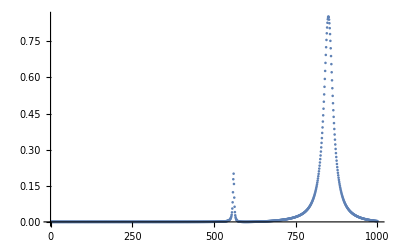

```mathematica
data1=Table[Eff[(i/10)*10^3,RLlist[[1]]],{i,1,1000,1}];
ListPlot[data1,PlotRange->All]
```

```mathematica
{Max[data1],Position[data1,Max[data1]]}
```

{0.853054,{{850}}}

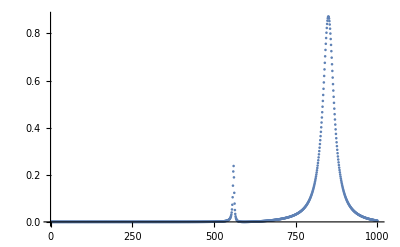

{0.87176,{{850}}}

```mathematica
data2=Table[Eff[(i/10)*10^3,RLlist[[2]]],{i,1,1000,1}];
ListPlot[data2,PlotRange->All]
{Max[data2],Position[data2,Max[data2]]}
```

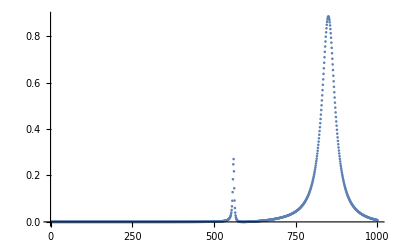

{0.884566,{{850}}}

```mathematica
data3=Table[Eff[(i/10)*10^3,RLlist[[3]]],{i,1,1000,1}];
ListPlot[data3,PlotRange->All]
{Max[data3],Position[data3,Max[data3]]}
```

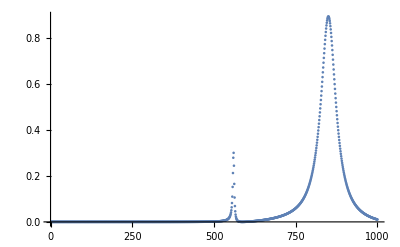

{0.893835,{{850}}}

```mathematica
data4=Table[Eff[(i/10)*10^3,RLlist[[4]]],{i,1,1000,1}];
ListPlot[data4,PlotRange->All]
{Max[data4],Position[data4,Max[data4]]}
```

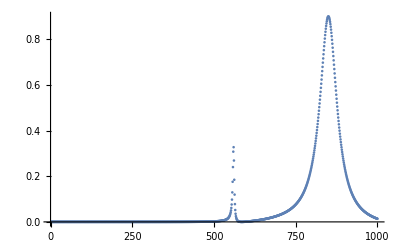

{0.900816,{{850}}}

```mathematica
data5=Table[Eff[(i/10)*10^3,RLlist[[5]]],{i,1,1000,1}];
ListPlot[data5,PlotRange->All]
{Max[data5],Position[data5,Max[data5]]}
```

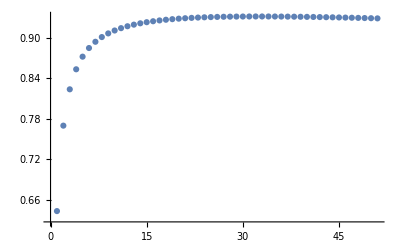

{0.931345,{{32}}}

```mathematica
data6=Table[Eff[85*10^3,1/5+i],{i,0,10,1/5}];
ListPlot[data6,PlotRange->All]
{Max[data6],Position[data6,Max[data6]]}
```

```mathematica
Eff[85*10^3,1/5+1/5*31]
```

0.931345

```mathematica
(1/5+1/5*31)//N
```

6.4